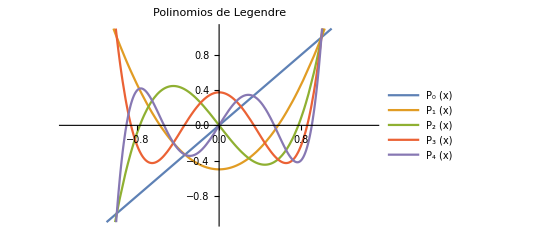

```mathematica
poliLegendre[n_] = LegendreP[n, x];
plot1 = Plot[Evaluate[poliLegendre/@Range[5]],{x, -5,5}, PlotLabel->Style["Polinomios de Legendre", FontSize-> 14, Black], PlotRange->{{-1.5,1.5},{-1.1,1.1}}, PlotLegends->{"P_0 (x)","P_1 (x)", "P_2 (x)","P_3 (x)", "P_4 (x)"}]
```

```mathematica
Export["plot_Legendre_01.eps",plot1]
```

plot_Legendre_01.eps

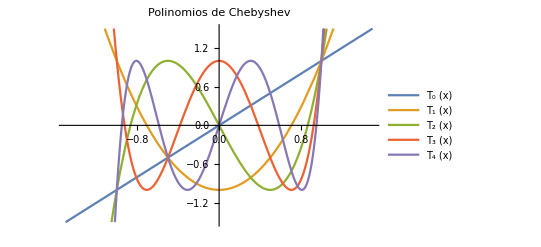

```mathematica
poliChebyshev[n_] = ChebyshevT[n, x];
plot2 = Plot[Evaluate[poliChebyshev/@Range[5]],{x, -5,5}, PlotLabel->Style["Polinomios de Chebyshev", FontSize-> 14, Black], PlotRange->{{-1.5,1.5},{-1.5,1.5}}, PlotLegends->{"T_0 (x)","T_1 (x)", "T_2 (x)","T_3 (x)", "T_4 (x)"}]
```

```mathematica
Export["plot_Chebyshev_01.eps",plot2]
```

plot_Chebyshev_01.eps

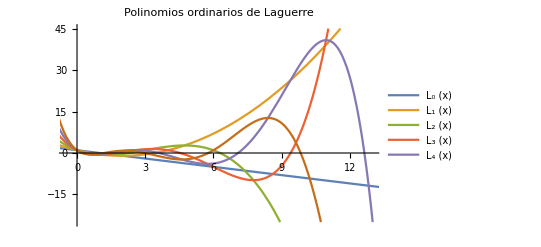

```mathematica
poliLaguerre[n_] = LaguerreL[n, x];
plot3 = Plot[Evaluate[poliLaguerre/@Range[6]],{x, -1,20}, PlotLabel->Style["Polinomios ordinarios de Laguerre", FontSize-> 14, Black], PlotRange->{{-0.5,13},{-25,45}}, PlotLegends->{"L_0 (x)","L_1 (x)", "L_2 (x)","L_3 (x)", "L_4 (x)"}]
```

```mathematica
Export["plot_Laguerre_01.eps",plot3]
```

plot_Laguerre_01.eps

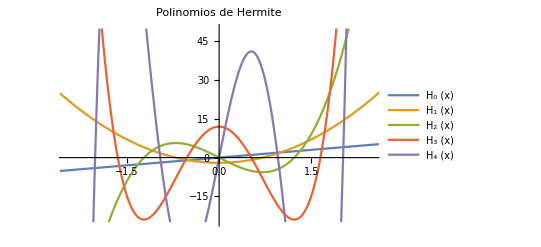

```mathematica
poliHermite[n_] = HermiteH[n, x];
plot4 = Plot[Evaluate[poliHermite/@Range[5]],{x, -5,5}, PlotLabel->Style["Polinomios de Hermite", FontSize-> 14, Black], PlotRange->{{-2.5, 2.5},{-25,50}}, PlotLegends->{"H_0 (x)","H_1 (x)", "H_2 (x)","H_3 (x)", "H_4 (x)"}]
```

```mathematica
Export["plot_Hermite_01.eps",plot4]
```

plot_Hermite_01.eps

```mathematica
Directory[]
```

C:\Users\gusto\Documents